```mathematica
SetDirectory[NotebookDirectory[]];
```

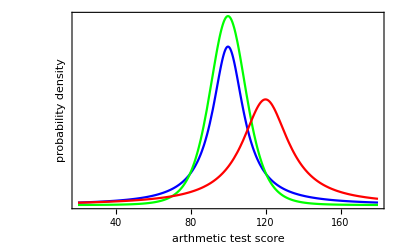

```mathematica
μ = 100;
σ1 = 10;
ν1 = 1;
ν2= 5;
σ2 = 15;
g4=Plot[{PDF[StudentTDistribution[μ,σ1,ν1],x],PDF[StudentTDistribution[μ,σ1,ν2],x],PDF[StudentTDistribution[120,σ2,ν1],x]},{x,20,180},PlotRange->Full,Frame->{True,True,False,False},BaseStyle->Medium,FrameLabel->{"arthmetic test score","probability density"},Axes->{False,False},FrameTicks->{True,False},PlotStyle->{Blue,Green,Red}]
```

```mathematica
Export["Distributions_tArithmeticExposition.pdf",g4]
```

Distributions_tArithmeticExposition.pdf